```mathematica
a[B_]:=abg(1-Dt/(B-B0)); cond={B0->0,Dt->1,abg->1}
```

{B0→0,Dt→1,abg→1}

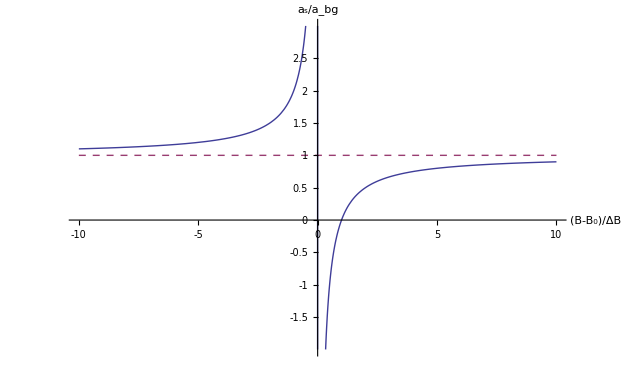

```mathematica
diag=Plot[{a[B]/.cond,abg/.cond},{B,-10,10},AxesLabel->{"(B-B_0)/ΔB","a_s/a_bg"},AxesOrigin->{0,0},LabelStyle->Directive[Bold,Larger], PlotRange->{-2,3},Ticks->{{-10,-5,0,5,10},{-1.5,-1,-0.5,0,0.5,1,1.5,2,2.5}},PlotStyle->{Thick,Dashed}]
```

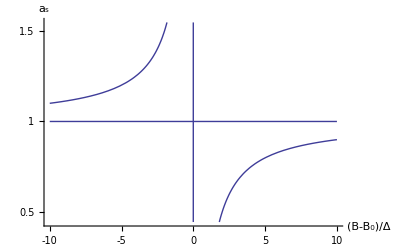

```mathematica
Show[diag,AxesLabel->{"(B-B_0)/Δ","a_s"},AxesOrigin->{0,0},LabelStyle->Directive[Bold,Larger], PlotRange->2,Ticks->{{-10,-5,0,5,10},{-1,-0.5,0,0.5,1,1.5}}]
```